```mathematica
Select[Keys[allGraphs4],IsomorphicGraphQ[allGraphs4[#,"graph"],CycleGraph[4]]&]
```

{328,280,120}

```mathematica
Select[Keys[allGraphs4],IsomorphicGraphQ[allGraphs4[#,"graph"],VertexAdd[CycleGraph[3],4]]&]
```

{333,273,109,13}

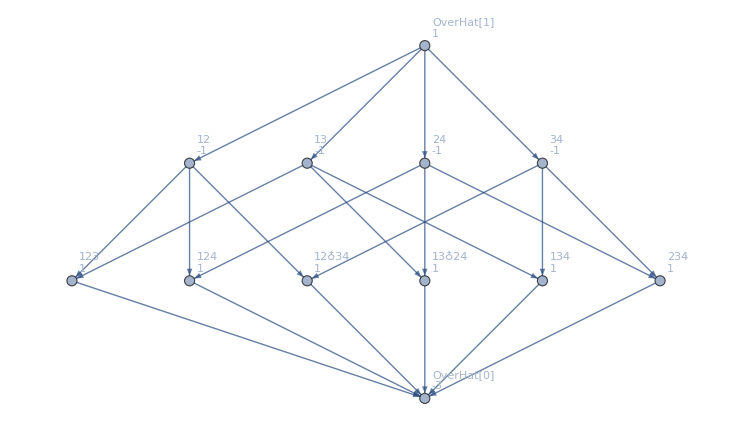

```mathematica
MobiusGraph5[328,allGraphs4]
```

```mathematica
EdgeList[MobiusGraph5[328,allGraphs4]]
```

{n123x4->n1234,n124x3->n1234,n12x34->n1234,n134x2->n1234,n13x24->n1234,n1x234->n1234,n12x3x4->n123x4,n13x2x4->n123x4,n12x3x4->n124x3,n1x24x3->n124x3,n12x3x4->n12x34,n1x2x34->n12x34,n13x2x4->n134x2,n1x2x34->n134x2,n13x2x4->n13x24,n1x24x3->n13x24,n1x24x3->n1x234,n1x2x34->n1x234,n1x2x3x4->n12x3x4,n1x2x3x4->n13x2x4,n1x2x3x4->n1x24x3,n1x2x3x4->n1x2x34}

```mathematica
VertexList[MobiusGraph5[328,allGraphs4]]
```

{n123x4,n124x3,n12x34,n134x2,n13x24,n1x234,n1x2x3x4,n1234,n12x3x4,n13x2x4,n1x24x3,n1x2x34}

```mathematica
Select[VertexList[MobiusGraph5[328,allGraphs4]],SymbolName[#]≠"n1x2x3x4"&]
```

{n123x4,n124x3,n12x34,n134x2,n13x24,n1x234,n1234,n12x3x4,n13x2x4,n1x24x3,n1x2x34}

```mathematica
DeleteDuplicates[Flatten[With[{g=MobiusGraph5[K4Key,allGraphs4]},Map[EdgeList[NeighborhoodGraph[g,#]]&,Select[VertexList[MobiusGraph5[328,allGraphs4]],SymbolName[#]≠"n1x2x3x4"&]]]]]
```

{n123x4->n1234,n12x3x4->n123x4,n13x2x4->n123x4,n1x23x4->n123x4,n124x3->n1234,n12x3x4->n124x3,n14x2x3->n124x3,n1x24x3->n124x3,n12x34->n1234,n12x3x4->n12x34,n1x2x34->n12x34,n134x2->n1234,n13x2x4->n134x2,n14x2x3->n134x2,n1x2x34->n134x2,n13x24->n1234,n13x2x4->n13x24,n1x24x3->n13x24,n1x234->n1234,n1x23x4->n1x234,n1x24x3->n1x234,n1x2x34->n1x234,n14x23->n1234,n1x2x3x4->n12x3x4,n1x2x3x4->n13x2x4,n1x2x3x4->n1x24x3,n1x2x3x4->n1x2x34}

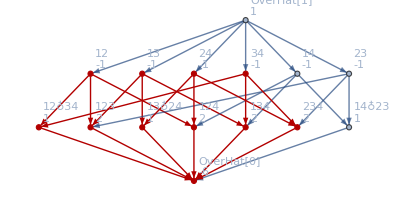

```mathematica
With[{
g=MobiusGraph5[K4Key,allGraphs4],
h=MobiusGraph5[328,allGraphs4]
},
With[
{max=ToString[First[Sort[VertexList[g],StringCount[SymbolName[#1],"x"]>StringCount[SymbolName[#2],"x"]&]]]},
Graph[g,GraphHighlight->DeleteDuplicates[Flatten[Map[Table[{#,kk,DirectedEdge[#,kk]},{kk,VertexOutComponent[g,#]}]&,Select[VertexList[h],SymbolName[#]≠max&]]]]]
]
]
```

```mathematica
TriangleNumber[k_]:=k(k+1)/2
```

```mathematica
TriangleNumber[3]
```

6

```mathematica
FromDigits[Table[1,{k,TriangleNumber[VertexCount[allGraphs4[0,"graph"]]-1]}],3]
```

364

```mathematica
K4Key
```

364

```mathematica
Descendants[g_,v_]:=Block[{comp=Select[VertexOutComponent[g,v,1],ToString[#]≠ToString[v]&], edges={},current},
While[comp ≠ {},
current=First[comp];
comp=Rest[comp];
edges=Join[edges,{v,current,DirectedEdge[v,current]}];
edges=Join[edges,Descendants[g,current]]
];
edges
]
```

```mathematica
Select[VertexOutComponent[MobiusGraph5[K5Key,allGraphs5],n1x2x3x45],ToString[#]≠ToString[n1x2x3x45]&]
```

{n12x3x45,n13x2x45,n1x23x45,n145x2x3,n1x245x3,n1x2x345,n123x45,n1245x3,n12x345,n1345x2,n13x245,n145x23,n1x2345,n12345}

```mathematica
Descendants[MobiusGraph5[K4Key,allGraphs4],n14x23]
```

{n14x23,n1234,n14x23->n1234}

```mathematica
ShowDamage[allGraphs_,key_]:=Block[
{
(* The Kx key is a rnage of 1s in ternary.  The length is a triangular number depending on the vertex count *)
kxKey=FromDigits[Table[1,{k,TriangleNumber[VertexCount[allGraphs[0,"graph"]]-1]}],3],
result=Null
},
With[{
(* g is the complete lattice graph*)
g=MobiusGraph5[kxKey,allGraphs],
h=MobiusGraph5[key,allGraphs]
},
With[
{
(* max is the symbol at the top of the mobius graph, we compute it since we want to independent of the number of nodes *)
max=ToString[First[Sort[VertexList[g],StringCount[SymbolName[#1],"x"]>StringCount[SymbolName[#2],"x"]&]]]
},
result=Graph[
g,
GraphHighlight->DeleteDuplicates[Flatten[Map[Table[{#,kk},{kk,Descendants[g,#]}]&,Select[VertexList[h],SymbolName[#]≠max&]]]],
VertexStyle->Darker[Green]]
]
];
result
]
```

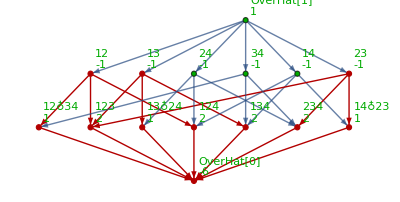

```mathematica
ShowDamage[allGraphs4,333]
```

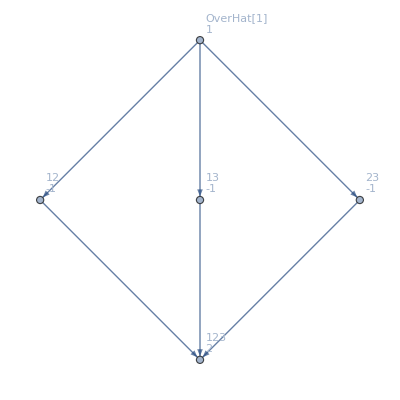
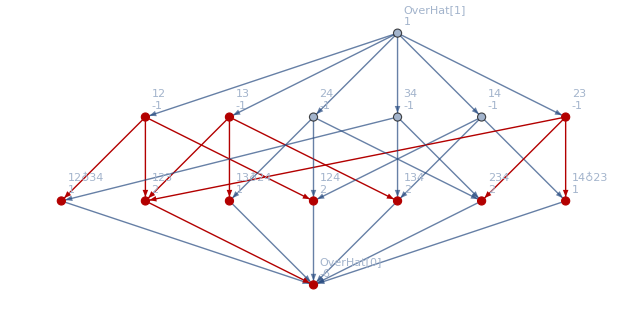

```mathematica
With[{
g=MobiusGraph5[K4Key,allGraphs4],
h=MobiusGraph5[333,allGraphs4]
},
{h,Graph[g,GraphHighlight->DeleteDuplicates[Flatten[Map[Table[{#,kk,DirectedEdge[#,kk]},{kk,VertexOutComponent[g,#]}]&,Select[VertexList[h],SymbolName[#]≠"n1x2x3x4"&]]]]]}
]
```

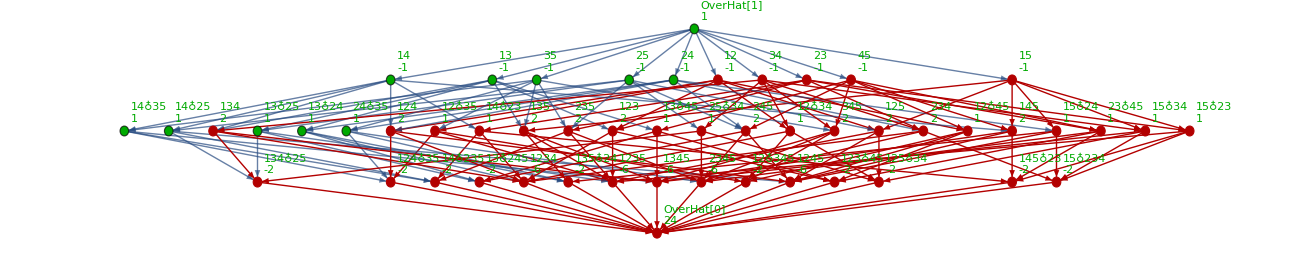

```mathematica
ShowDamage[allGraphs5,lambdaKey]
```

```mathematica
rep5=Table[allGraphs5[k,"colofour"]->SymbolToLabel2[allGraphs5[k,"colofour"]],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5→OverHat[1],v1x2x3x45→45,v1x2x35x4→35,v1x2x34x5→34,v1x2x345→345,v1x25x3x4→25,v1x25x34→25♁34,v1x24x3x5→24,v1x24x35→24♁35,v1x245x3→245,v1x23x4x5→23,v1x23x45→23♁45,v1x235x4→235,v1x234x5→234,v1x2345→2345,v15x2x3x4→15,v15x2x34→15♁34,v15x24x3→15♁24,v15x23x4→15♁23,v15x234→15♁234,v14x2x3x5→14,v14x2x35→14♁35,v14x25x3→14♁25,v14x23x5→14♁23,v14x235→14♁235,v145x2x3→145,v145x23→145♁23,v13x2x4x5→13,v13x2x45→13♁45,v13x25x4→13♁25,v13x24x5→13♁24,v13x245→13♁245,v135x2x4→135,v135x24→135♁24,v134x2x5→134,v134x25→134♁25,v1345x2→1345,v12x3x4x5→12,v12x3x45→12♁45,v12x35x4→12♁35,v12x34x5→12♁34,v12x345→12♁345,v125x3x4→125,v125x34→125♁34,v124x3x5→124,v124x35→124♁35,v1245x3→1245,v123x4x5→123,v123x45→123♁45,v1235x4→1235,v1234x5→1234,v12345→OverHat[0]}

```mathematica
allGraphs5[lambdaKey,"colofour"]/.rep5
```

```mathematica
allGraphs5[alfaKey,"graph"]->Labeled[(allGraphs5[alfaKey,"colofour"]/.rep5),Style[alfaKey,ColourForKey[allGraphs5,alfaKey]]]
```

-Graphics-→13+13♁24+13♁2535977

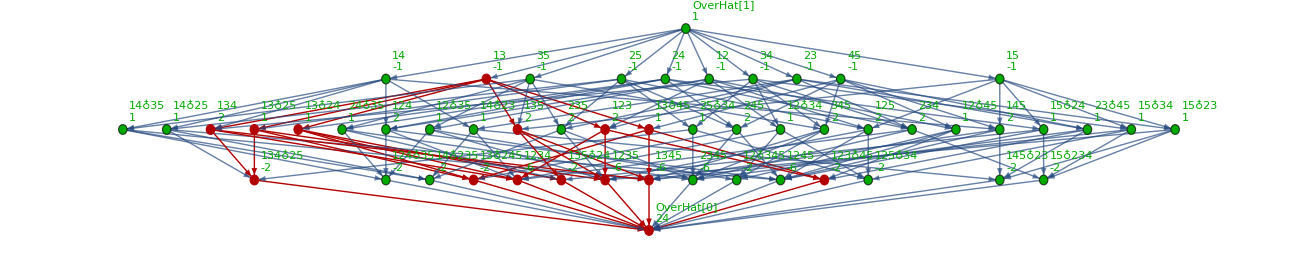

```mathematica
ShowDamage[allGraphs5,alfaKey]
```

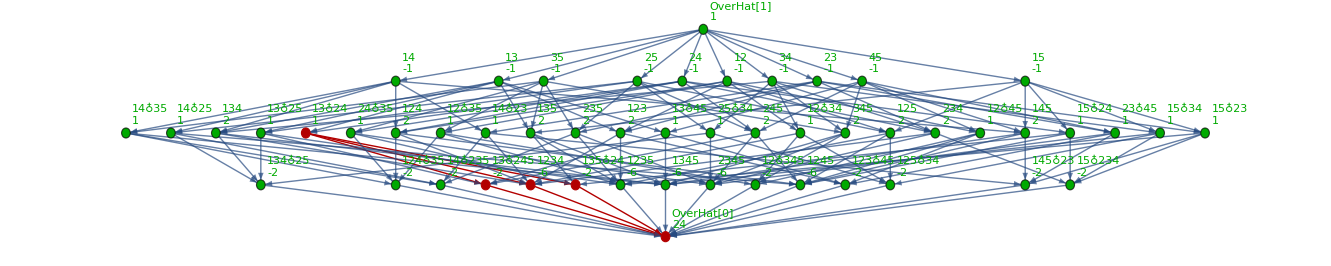

```mathematica
ShowDamage[allGraphs5,alfa1Key]
```

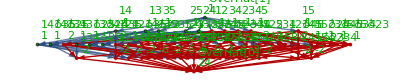

```mathematica
ShowDamage[allGraphs5,lambdaKey]
```

```mathematica
With[{
g=MobiusGraph5[K4Key,allGraphs4],
h=MobiusGraph5[328,allGraphs4]
},
DeleteDuplicates[Flatten[Map[Table[#->kk,{kk,VertexOutComponent[g,#]}]&,Select[VertexList[h],SymbolName[#]≠"n1x2x3x4"&]]]]
]
```

{n123x4→n123x4,n123x4→n1234,n124x3→n124x3,n124x3→n1234,n12x34→n12x34,n12x34→n1234,n134x2→n134x2,n134x2→n1234,n13x24→n13x24,n13x24→n1234,n1x234→n1x234,n1x234→n1234,n1234→n1234,n12x3x4→n12x3x4,n12x3x4→n12x34,n12x3x4→n123x4,n12x3x4→n124x3,n12x3x4→n1234,n13x2x4→n13x2x4,n13x2x4→n13x24,n13x2x4→n123x4,n13x2x4→n134x2,n13x2x4→n1234,n1x24x3→n1x24x3,n1x24x3→n13x24,n1x24x3→n124x3,n1x24x3→n1x234,n1x24x3→n1234,n1x2x34→n1x2x34,n1x2x34→n12x34,n1x2x34→n134x2,n1x2x34→n1x234,n1x2x34→n1234}

```mathematica
With[{
g=MobiusGraph5[K4Key,allGraphs4],
h=MobiusGraph5[328,allGraphs4]
},
Select[VertexList[h],SymbolName[#]≠"n1x2x3x4"&]
]
```

{n123x4,n124x3,n12x34,n134x2,n13x24,n1x234,n1234,n12x3x4,n13x2x4,n1x24x3,n1x2x34}

```mathematica
ShowDamage[allGraphs4,333]
```

-Graphics-